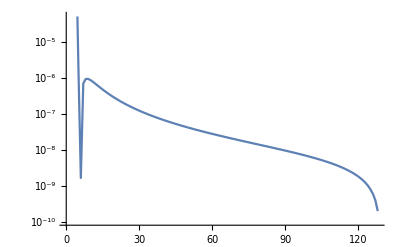

-Graphics-

```mathematica
spectrumWindow[x_]:=x*Table[BlackmanHarrisWindow[t-0.5],{t,0,1,1/(Length[x]-1)}]
fourierSpectrum[x_]:=Abs[Take[Fourier[x],Length[x]/2+1]]
toDb[x_]:=20Log10[x]/.Indeterminate->-100
scaleDbForImage[X_]:=Clip[X+100,{0,100}]/100
colourFunction[x_]:={7/12,1-x,x}
dcSpectrum=fourierSpectrum[spectrumWindow[Normalize[Table[1,{t,1,2^8}]]]];
ListLogPlot[dcSpectrum,Joined->True]
Image[{colourFunction/@scaleDbForImage[toDb[dcSpectrum]]},ImageSize->Full,ColorSpace->"HSB"]
```

```mathematica
sineSweep[length_,startF_,endF_,sampleRate_]:=Module[{output,i,phase,frequency,f1,f2,phaseIncrement},output=Range[length];
phase=0;
f1=N[2π startF/sampleRate];
f2=N[2 π endF/sampleRate];
For[i=1,i≤length,i++,output[[i]]=Sin[phase];
frequency=f1+(f2-f1)*(i/length);
phaseIncrement=frequency;
phase+=phaseIncrement;];
output]
(*ListPlay[sineSweep[48000,20,2000,48000],SampleRate->48000]*)

(*generate a sine sweep*)
sampleRate=48000;
fftLength = 4096;
fftStride = 64
verticalResolution = 300;
minFrequency = 50;
maxFrequency = sampleRate / 2;
ss1=sineSweep[1*sampleRate,20,20000,sampleRate];
ss2=sineSweep[1*sampleRate,80,80000,sampleRate];
bass=Table[Sin[60 N[2 π] t/sampleRate],{t,1,sampleRate}];
ss=ss1+ss2+bass;

(*partition the sine sweep with offset*)
windows=Partition[ss,fftLength,fftStride];

(* find N exponential values between min and max*)
expArray[n_,min_,max_]:=min N[(max/min)^(#/(n-1))]&/@Range[0,n-1]

(* find the interpolated non-integer fft bin at frequency f, with DC bin as bin zero *)
fftBinZeroDC[f_,fftLength_,sampleRate_]:=f / (sampleRate/fftLength)

linearFFTSpectrumToExpSpectrum[x_,fftLength_,sampleRate_,outputBins_]:=Interpolation[x]/@expArray[verticalResolution,
fftBinZeroDC[minFrequency,fftLength,sampleRate],
fftBinZeroDC[maxFrequency,]
]

(*find the spectrum of each partition*)
spectrogramColumn[x_]:=colourFunction/@Reverse[scaleDbForImage[linearFFTSpectrumToExpSpectrum[toDb[fourierSpectrum[spectrumWindow[x]]]]]]
spectrogramData=Transpose[spectrogramColumn/@windows];
toHSBImage[X_]:=Image[X,ColorSpace->"HSB"]
toHSBImage[spectrogramData]
```

Image::imgarray: The specified argument {{49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,49/144,«637»},{«1»},{1/100 «1»,«50»}} should be an array of rank 2 or 3 with machine-sized numbers.

Image[{1},ColorSpace→HSB]
 |  |  |  |